# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-11-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-03-19

```mathematica
states=Union[seqData[[All,2]]]
```

{California,Colorado,Connecticut,Florida,Georgia,Illinois,Massachusetts,Michigan,Minnesota,New Jersey,New York,North Carolina,Oregon,Pennsylvania,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{California,Colorado,Connecticut,Florida,Georgia,Illinois,Massachusetts,Michigan,Minnesota,New Jersey,New York,North Carolina,Oregon,Pennsylvania,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{California→{{2022-03-05,198},{2022-03-06,151},{2022-03-07,306},{2022-03-08,199},{2022-03-09,225},{2022-03-10,196},{2022-03-11,192},{2022-03-12,93},{2022-03-13,81},{2022-03-14,76},{2022-03-15,12},{2022-03-16,14},{2022-03-17,4},{2022-03-18,7},{2022-03-19,0}},Colorado→{{2022-03-05,63},{2022-03-06,37},{2022-03-07,129},{2022-03-08,123},{2022-03-09,91},{2022-03-10,64},{2022-03-11,62},{2022-03-12,41},{2022-03-13,38},{2022-03-14,85},{2022-03-15,44},{2022-03-16,0},{2022-03-17,0},{2022-03-18,0},{2022-03-19,0}},Connecticut→{{2022-03-05,23},{2022-03-06,14},{2022-03-07,71},{2022-03-08,71},{2022-03-09,55},{2022-03-10,50},{2022-03-11,42},{2022-03-12,27},{2022-03-13,27},{2022-03-14,57},{2022-03-15,42},{2022-03-16,46},{2022-03-17,6},{2022-03-18,5},{2022-03-19,4}},Florida→{{2022-03-05,118},{2022-03-06,97},{2022-03-07,146},{2022-03-08,107},{2022-03-09,91},{2022-03-10,103},{2022-03-11,96},{2022-03-12,58},{2022-03-13,24},{2022-03-14,29},{2022-03-15,6},{2022-03-16,9},{2022-03-17,1},{2022-03-18,12},{2022-03-19,0}},Georgia→{{2022-03-05,29},{2022-03-06,18},{2022-03-07,43},{2022-03-08,24},{2022-03-09,14},{2022-03-10,26},{2022-03-11,14},{2022-03-12,12},{2022-03-13,2},{2022-03-14,9},{2022-03-15,5},{2022-03-16,0},{2022-03-17,0},{2022-03-18,2},{2022-03-19,0}},Illinois→{{2022-03-05,60},{2022-03-06,60},{2022-03-07,86},{2022-03-08,70},{2022-03-09,59},{2022-03-10,59},{2022-03-11,39},{2022-03-12,23},{2022-03-13,29},{2022-03-14,43},{2022-03-15,6},{2022-03-16,13},{2022-03-17,1},{2022-03-18,14},{2022-03-19,1}},Massachusetts→{{2022-03-05,109},{2022-03-06,120},{2022-03-07,235},{2022-03-08,228},{2022-03-09,154},{2022-03-10,188},{2022-03-11,147},{2022-03-12,84},{2022-03-13,76},{2022-03-14,217},{2022-03-15,166},{2022-03-16,176},{2022-03-17,9},{2022-03-18,3},{2022-03-19,0}},Michigan→{{2022-03-05,30},{2022-03-06,26},{2022-03-07,52},{2022-03-08,46},{2022-03-09,33},{2022-03-10,29},{2022-03-11,29},{2022-03-12,21},{2022-03-13,7},{2022-03-14,11},{2022-03-15,8},{2022-03-16,2},{2022-03-17,0},{2022-03-18,6},{2022-03-19,0}},Minnesota→{{2022-03-05,10},{2022-03-06,15},{2022-03-07,81},{2022-03-08,10},{2022-03-09,19},{2022-03-10,14},{2022-03-11,10},{2022-03-12,4},{2022-03-13,8},{2022-03-14,10},{2022-03-15,1},{2022-03-16,3},{2022-03-17,0},{2022-03-18,2},{2022-03-19,0}},New Jersey→{{2022-03-05,58},{2022-03-06,39},{2022-03-07,110},{2022-03-08,89},{2022-03-09,61},{2022-03-10,38},{2022-03-11,25},{2022-03-12,17},{2022-03-13,22},{2022-03-14,36},{2022-03-15,20},{2022-03-16,14},{2022-03-17,1},{2022-03-18,5},{2022-03-19,4}},New York→{{2022-03-05,82},{2022-03-06,87},{2022-03-07,172},{2022-03-08,147},{2022-03-09,160},{2022-03-10,133},{2022-03-11,112},{2022-03-12,62},{2022-03-13,76},{2022-03-14,131},{2022-03-15,86},{2022-03-16,108},{2022-03-17,72},{2022-03-18,81},{2022-03-19,28}},North Carolina→{{2022-03-05,62},{2022-03-06,58},{2022-03-07,108},{2022-03-08,60},{2022-03-09,46},{2022-03-10,39},{2022-03-11,28},{2022-03-12,20},{2022-03-13,5},{2022-03-14,21},{2022-03-15,14},{2022-03-16,4},{2022-03-17,1},{2022-03-18,0},{2022-03-19,0}},Oregon→{{2022-03-05,17},{2022-03-06,8},{2022-03-07,39},{2022-03-08,20},{2022-03-09,16},{2022-03-10,10},{2022-03-11,6},{2022-03-12,6},{2022-03-13,6},{2022-03-14,6},{2022-03-15,1},{2022-03-16,2},{2022-03-17,1},{2022-03-18,0},{2022-03-19,0}},Pennsylvania→{{2022-03-05,67},{2022-03-06,44},{2022-03-07,93},{2022-03-08,72},{2022-03-09,52},{2022-03-10,50},{2022-03-11,36},{2022-03-12,27},{2022-03-13,17},{2022-03-14,11},{2022-03-15,9},{2022-03-16,1},{2022-03-17,0},{2022-03-18,0},{2022-03-19,0}},Tennessee→{{2022-03-05,12},{2022-03-06,8},{2022-03-07,10},{2022-03-08,21},{2022-03-09,7},{2022-03-10,14},{2022-03-11,9},{2022-03-12,1},{2022-03-13,0},{2022-03-14,6},{2022-03-15,10},{2022-03-16,1},{2022-03-17,0},{2022-03-18,0},{2022-03-19,1}},Texas→{{2022-03-05,97},{2022-03-06,108},{2022-03-07,103},{2022-03-08,59},{2022-03-09,40},{2022-03-10,39},{2022-03-11,30},{2022-03-12,24},{2022-03-13,16},{2022-03-14,12},{2022-03-15,3},{2022-03-16,6},{2022-03-17,0},{2022-03-18,6},{2022-03-19,0}},Utah→{{2022-03-05,22},{2022-03-06,13},{2022-03-07,39},{2022-03-08,29},{2022-03-09,15},{2022-03-10,18},{2022-03-11,11},{2022-03-12,4},{2022-03-13,5},{2022-03-14,23},{2022-03-15,6},{2022-03-16,1},{2022-03-17,0},{2022-03-18,2},{2022-03-19,0}},Virginia→{{2022-03-05,41},{2022-03-06,45},{2022-03-07,45},{2022-03-08,28},{2022-03-09,25},{2022-03-10,19},{2022-03-11,30},{2022-03-12,17},{2022-03-13,13},{2022-03-14,11},{2022-03-15,5},{2022-03-16,0},{2022-03-17,0},{2022-03-18,1},{2022-03-19,0}},Washington→{{2022-03-05,83},{2022-03-06,61},{2022-03-07,76},{2022-03-08,62},{2022-03-09,70},{2022-03-10,82},{2022-03-11,60},{2022-03-12,32},{2022-03-13,27},{2022-03-14,131},{2022-03-15,62},{2022-03-16,72},{2022-03-17,27},{2022-03-18,55},{2022-03-19,15}},Wisconsin→{{2022-03-05,28},{2022-03-06,21},{2022-03-07,61},{2022-03-08,43},{2022-03-09,26},{2022-03-10,45},{2022-03-11,41},{2022-03-12,20},{2022-03-13,7},{2022-03-14,47},{2022-03-15,16},{2022-03-16,16},{2022-03-17,8},{2022-03-18,16},{2022-03-19,7}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

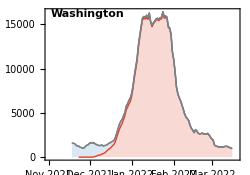

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

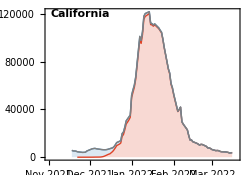
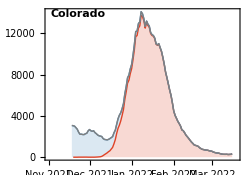
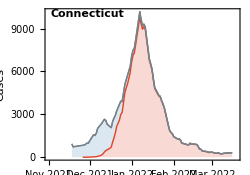
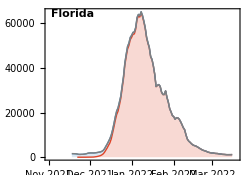
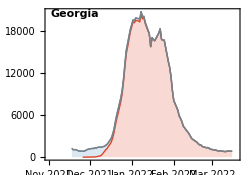
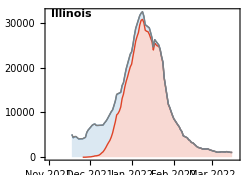
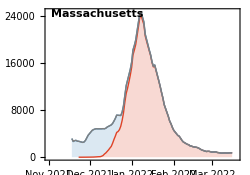
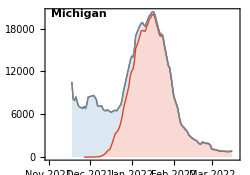
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png